```mathematica
seq={5,16,24,72};
```

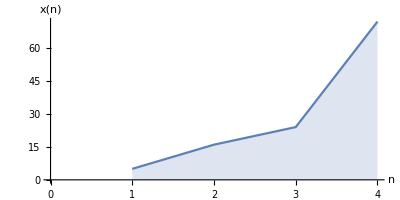

```mathematica
ListLinePlot[seq,Filling->Axis,LabelStyle->Medium,AspectRatio->1/2,AxesLabel->{n,x[n]}]
```

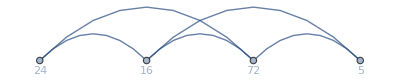

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{5->16,5->72,16->24,16->72,24->72},VertexLabels->"Name",GraphLayout->"LinearEmbedding",DirectedEdges->False]
```

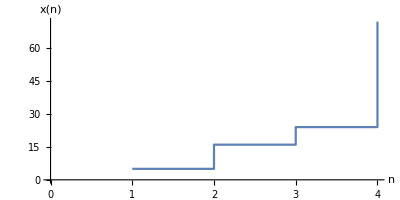

```mathematica
ListLinePlot[seq,InterpolationOrder->0,LabelStyle->Medium,AspectRatio->1/2,AxesLabel->{n,x[n]}]
```

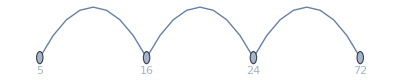

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[{5->16,16->24,24->72},VertexLabels->"Name",GraphLayout->"LinearEmbedding",DirectedEdges->False]
```